```mathematica
dir=NotebookDirectory[];
a=SetDirectory[dir]
date = DateString[Riffle[{"06","18"},"_"]]
```

D:\Curve Elasticity\Simulation\2026\jan\results\catenoid\horizontal1p

06_18

```mathematica
c=1
X[u_,v_]:={Cosh[v/c] Cos[u],Cosh[v/c] Sin[u],v};
uu=Import["uu_2_26_"<>date<>".txt","Table"];
vv=Import["vv_2_26_"<>date<>".txt","Table"];
uu=Flatten[uu];
vv=Flatten[vv];
points=MapThread[X,{uu,vv}];
V2k=Graphics3D[{Yellow,Thickness[0.01],Line[points]},Boxed->False];

V3=ParametricPlot3D[X[u,v],{u,0,2Pi},{v,-1.5,1.5},PlotStyle->Directive[LightRed]];

Show[ V3,V2k,PlotRange->All]
```

1

-Graphics3D-

```mathematica
σ
```

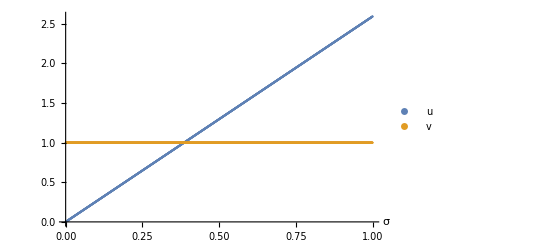

```mathematica
ListPlot[{Reverse[uu],Reverse[vv]},AxesLabel->{σ},PlotLegends->{u,v},DataRange->{0,1}]
ListPlot[vv];
```

```mathematica
Export["D:\\Curve Elasticity\\Simulation\\2026\\jan\\results\\catenoid\\horizontal1p\\uv.png",%146,"PNG"]
```

D:\Curve Elasticity\Simulation\2026\jan\results\catenoid\horizontal1p\uv.png

```mathematica
Cosh[1] //N
```

1.54308

```mathematica
6.28/2.6
```

2.41538

1

```mathematica
X[u_,v_]:={Cosh[v/c] Cos[u],Cosh[v/c] Sin[u],v};
uu=Import["D:\\Curve Elasticity\\Simulation\\w phi\\catenoid\\vertical\\uu_2_25_07_30.txt","Table"];
vv=Import["D:\\Curve Elasticity\\Simulation\\w phi\\catenoid\\vertical\\vv_2_25_07_30.txt","Table"];

uu=Flatten[uu];
vv=Flatten[vv];
points=MapThread[X,{uu,vv}];
V3k=Graphics3D[{White,Thick,Line[points]},Boxed->False];
```

```mathematica
Sin[Pi/4] //N
```

0.707107

```mathematica
c=1
X[u_,v_]:={Cosh[v/c] Cos[u],Cosh[v/c] Sin[u],v};
(*First derivatives*)
Xu=D[X[u,v],u]
Xv=D[X[u,v],v]

(*Second derivatives*)
Xuu=D[X[u,v],{u,2}];
Xuv=D[Xu,v];
Xvv=D[X[u,v],{v,2}];

(*Normal vector to surface*)
nVec=Cross[Xu,Xv]//Simplify 
n2=Sqrt[nVec.nVec]  //FullSimplify;
n2=(Cosh[v])^2;
nVec=nVec/n2 //FullSimplify;
```

1

{-Cosh[v] Sin[u],Cos[u] Cosh[v],0}

{Cos[u] Sinh[v],Sin[u] Sinh[v],1}

{Cos[u] Cosh[v],Cosh[v] Sin[u],-Cosh[v] Sinh[v]}

```mathematica
(*First fundamental form:g_ij= <X_i,X_j>*)
g11=Simplify[Xu.Xu];
g12=Simplify[Xu.Xv];
g22=Simplify[Xv.Xv];
gMat={{g11,g12},{g12,g22}}


(*Second fundamental form:b_ij= <X_ij,n>*)
b11=Simplify[Xuu.nVec];
b12=Simplify[Xuv.nVec];
b22=Simplify[Xvv.nVec];
bMat={{b11,b12},{b12,b22}}

H=1/2*Tr[Inverse[gMat].bMat]
K=Det[Inverse[gMat].bMat]
```

{{Cosh[v]^2,0},{0,Cosh[v]^2}}

{{-1,0},{0,1}}

0

-Sech[v]^4

```mathematica
u0=x;
v0=0;
V3=ParametricPlot3D[X[u,v],{u,0,2Pi},{v,-1.5,1.5},PlotStyle->Directive[LightRed]];
Vl=ParametricPlot3D[X[u0,v0],{x,0,1},PlotStyle->Yellow];
Show[V3,Vl]
```

-Graphics3D-

```mathematica
X[u_,v_]:={Cosh[v/c] Cos[u],Cosh[v/c] Sin[u],v};
NN= nVec/.{u->u0,v->v0} ;
X0 = X[ u0,v0];
X01 = D[X0,x] ;
g1=Sqrt[X01.X01] //Simplify;
Xs=X01/g1;
Xss = D[Xs,x]/g1;
nn=Cross[NN,Xs] //Simplify;

ns=D[nn,x]/g1;
kg=Xss.nn  //Simplify  
kn = Xss.NN //Simplify  
taug = ns.NN //Simplify
```

0

-1

0

(2 (-1+ⅇ) √ⅇ)/(1+ⅇ)^2

-(4 ⅇ)/(1+ⅇ)^2

0

```mathematica
th = Pi/3 //N
kb = 1/(Sin[th]) //N
kgb = kb Cos[th] //N
kg = Cot[th] //N

(kg-kgb);
0-kgb;
```

1.0472

1.1547

0.57735

0.57735

```mathematica
NumberForm[th,16]
```

1.047197551196598

```mathematica
NumberForm[kb,16]
```

1.154700538379252

```mathematica
NumberForm[kgb,16]
```

0.577350269189626

```mathematica
NumberForm[kb,16]
```

1.154700538379252

```mathematica
N[2/(√3)]
```

1.1547

```mathematica
NumberForm[1.1547005383792517,16]
```

1.154700538379252

```mathematica
NumberForm[1.1808719834468142,16]
```

1.180871983446814

```mathematica
NumberForm[1.1883951057781212,16]
```

1.188395105778121